## Выполнил: Шульжик Дмитрий 4 курс, 1 группа

## Матрица системы

```mathematica
A = {{1,-1,1},{1,1,-1},{0,-1,2}};
A//TableForm
```

1 | -1 | 1
1 | 1 | -1
0 | -1 | 2

### Собственные значения

```mathematica
Eigenvalues[A]
```

{2,1,1}

```mathematica
X[t_] = {x[t],y[t],z[t]}
```

{x[t],y[t],z[t]}

```mathematica
X'[t]==A.X[t]
```

{x'[t],y'[t],z'[t]}=={x[t]-y[t]+z[t],x[t]+y[t]-z[t],-y[t]+2 z[t]}

```mathematica
solution = DSolve[%,{x,y,z},t]
```

{{x→Function[{t},-ⅇ^t (-2+ⅇ^t-t) C[1]-ⅇ^t (-1+ⅇ^t) C[2]+ⅇ^t (-2+2 ⅇ^t-t) C[3]],y→Function[{t},ⅇ^t t C[1]+ⅇ^t C[2]-ⅇ^t t C[3]],z→Function[{t},-ⅇ^t (-1+ⅇ^t-t) C[1]-ⅇ^t (-1+ⅇ^t) C[2]+ⅇ^t (-1+2 ⅇ^t-t) C[3]]}}

#### Задание 2.

Найти  положения  равновесия,  определить  их  характер  и нарисовать  фазовые  траектории 
линеаризованных  систем  в  окрестности положений равновесия для автономных систем

-Graphics-

```mathematica
Subscript[f, 1][x_,y_]=ⅇ^(x^2-y)-ⅇ^(2x)
Subscript[f, 2][x_,y_]=-x-2y-y^2
```

-ⅇ^(2 x)+ⅇ^(x^2-y)

-x-2 y-y^2

```mathematica
stabilityPoints = Solve[{Subscript[f, 1][x,y]==0,Subscript[f, 2][x,y]==0},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1,y→-1},{x→0,y→0},{x→1/2 (3-ⅈ √3),y→1/2 (-3-ⅈ √3)},{x→1/2 (3+ⅈ √3),y→1/2 (-3+ⅈ √3)}}

```mathematica
jacobian = {{D[(Subscript[f, 1][x,y]),x],D[(Subscript[f, 1][x,y]),y]},{D[(Subscript[f, 2][x,y]),x],D[(Subscript[f, 2][x,y]),y]}};
jacobian//MatrixForm
```

(-2 ⅇ^(2 x)+2 ⅇ^(x^2-y) x | -ⅇ^(x^2-y)
-1 | -2-2 y)

```mathematica
jacobian/.stabilityPoints⟦1⟧//MatrixForm
```

(0 | -ⅇ^2
-1 | 0)

```mathematica
jacobian/.stabilityPoints⟦2⟧//MatrixForm
```

(-2 | -1
-1 | -2)

```mathematica
λ1 = Eigenvalues[jacobian/.stabilityPoints⟦1⟧]
λ2=Eigenvalues[jacobian/.stabilityPoints⟦2⟧]
```

{-ⅇ,ⅇ}

{-3,-1}

## В первой точке (0,-1) собственные значения не равны и больше нуля, следовательно точка (0, -1) фокус.

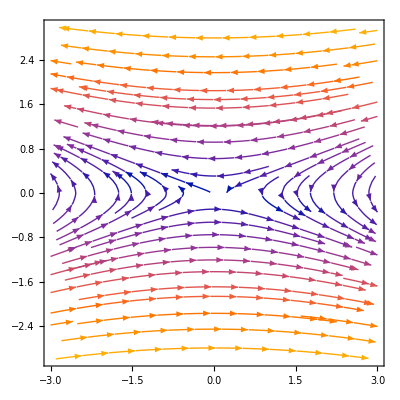

```mathematica
field1=(jacobian/.stabilityPoints⟦1⟧).{x,y};
StreamPlot[field1,{x,-3,3},{y,-3,3}]
```

## В точке (0,1) собственные значения равны и разных знаков, следовательно точка (0,1) седловая.

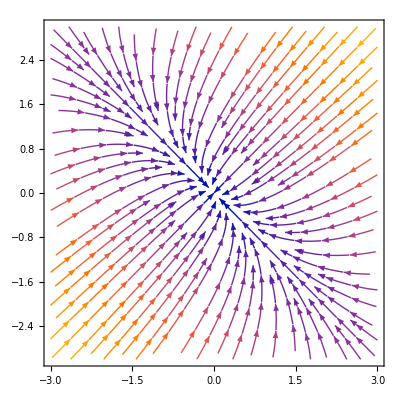

```mathematica
field2=(jacobian/.stabilityPoints⟦2⟧).{x,y};
StreamPlot[field2,{x,-3,3},{y,-3,3}]
```

```mathematica
stabilityPoints
```

{{x→0,y→-1},{x→0,y→1},{x→-(ⅈ π)/2,y→-√(1+ⅈ π)},{x→-(ⅈ π)/2,y→√(1+ⅈ π)},{x→(ⅈ π)/2,y→-√(1-ⅈ π)},{x→(ⅈ π)/2,y→√(1-ⅈ π)},{x→-ⅈ π,y→-√(1+2 ⅈ π)},{x→-ⅈ π,y→√(1+2 ⅈ π)}}